## Study of single UV limit with joint parameterisation

## Parameterisations

### Spherical

```mathematica
SphericalMap[x1_,x2_,x3_]:=Module[
{r=x1/(1-x1),θ=x2 π,ϕ=x3 2π,y,drOverdx=1/(x1-1)^2},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

```mathematica
Solve[rv-x1/(1-x1)==0,{x1}]
```

{{x1→rv/(rv+1)}}

```mathematica
InvSphericalMap[x_,y_,z_]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=r/(r+1);
drOverdx=1/(xr-1)^2;
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)drOverdx r^2 Sin[θ])
|>
]
```

Test the inverse map

```mathematica
Manipulate[{
(InvSphericalMap@@SphericalMap[x1,x2,x3]["vector"])["inv_jacobian"]*SphericalMap[x1,x2,x3]["jacobian"],
(InvSphericalMap@@SphericalMap[x1,x2,x3]["vector"])["xs"]-{x1,x2,x3}

}/.{x1->xm1,x2->xm2,x3->xm3},
{{xm1,0.2},0.,1.},
{{xm2,0.3},0.,1.},
{{xm3,0.4},0.,1.}
]
```

### Joint Spherical

```mathematica
JointSphericalMap2Loop[x1_,x2_,x3_,x4_,x5_,x6_]:=Module[
{r=x1/(1-x1),θ1=x2 π,ϕ1=x3 2π,θ2=x5 π,ϕ2=x6 2π,y,drOverdx=x1/(1-x1)^3,r1,r2},
r2=r x4 ;
r1=r-r2;
<|"vectorA"->{
r1 Sin[θ1]Cos[ϕ1],
r1 Sin[θ1]Sin[ϕ1],
r1 Cos[θ1]
},
"vectorB"->{
r2 Sin[θ2]Cos[ϕ2],
r2 Sin[θ2]Sin[ϕ2],
r2 Cos[θ2]
},
"jacobian"->(π) (2π)(π) (2π)drOverdx r1^2 Sin[θ1] r2^2 Sin[θ2]
|>
]
```

```mathematica
Solve[{x1/(1-x1)x4-rv2==0,x1/(1-x1)(1-x4)-rv1==0},{x1,x4}]
```

{{x1→(rv1+rv2)/(rv1+rv2+1),x4→rv2/(rv1+rv2)}}

```mathematica
InvJointSphericalMap2Loop[x1_,y1_,z1_,x2_,y2_,z2_]:=Module[
{r1,θ1,ϕ1,r2,θ2,ϕ2,y,drOverdx,xv1,xv4,sphCoord1,sphCoord2},
sphCoord1 = ToSphericalCoordinates[{x1,y1,z1}];
r1=sphCoord1⟦1⟧;
θ1=sphCoord1⟦2⟧;
ϕ1=sphCoord1⟦3⟧;
sphCoord2 = ToSphericalCoordinates[{x2,y2,z2}];
r2=sphCoord2⟦1⟧;
θ2=sphCoord2⟦2⟧;
ϕ2=sphCoord2⟦3⟧;
xv1=(r1+r2)/(r1+r2+1);
xv4=r2/(r1+r2);
drOverdx=xv1/(1-xv1)^3;
<|"xs"->{
xv1,
θ1/π,
Mod[ϕ1,2π]/(2π),
xv4,
θ2/π,
Mod[ϕ2,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)(π) (2π)drOverdx r1^2 Sin[θ1] r2^2 Sin[θ2])
|>
]
```

```mathematica
Manipulate[{
(InvJointSphericalMap2Loop@@Join[
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorA"],
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorB"]
])["inv_jacobian"]*JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["jacobian"],
(InvJointSphericalMap2Loop@@Join[
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorA"],
JointSphericalMap2Loop[x1,x2,x3,x4,x5,x6]["vectorB"]
])["xs"]-{x1,x2,x3,x4,x5,x6}
}/.{x1->xm1,x2->xm2,x3->xm3,x4->xm4,x5->xm5,x6->xm6},
{{xm1,0.2},0.,1.},
{{xm2,0.3},0.,1.},
{{xm3,0.4},0.,1.},
{{xm4,0.2},0.,1.},
{{xm5,0.3},0.,1.},
{{xm6,0.4},0.,1.}
]
```

### Spherical Log Weinzierl

```mathematica
SphericalLogMap[x1_,x2_,x3_,μ_]:=Module[
{r=Log[1+μ Tan[Pi/2x1]],θ=x2 π,ϕ=x3 2π,y,drOverdx=(μ π Sec[(π x1)/2]^2)/(2 (1+μ Tan[(π x1)/2]))},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

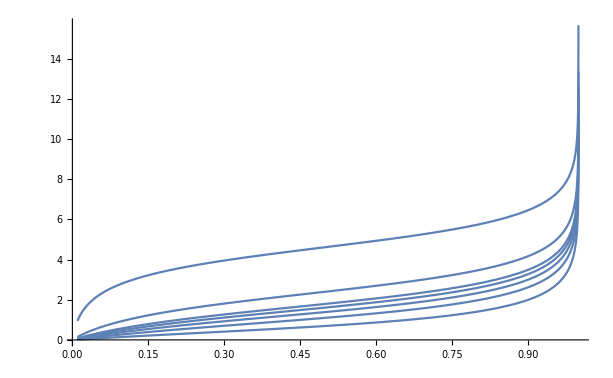

```mathematica
Plot[
Table[
Norm[SphericalLogMap[xr,0.2,0.4,μ]["vector"]],{μ,{1,2,3,4,5,10,100}}
],{xr,0.01,.99999},PlotRange->All]
```

```mathematica
InvSphericalLogMap[x_,y_,z_,μ_]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=(2 (ArcTan[(-1+Exp[r])/μ]))/π;
drOverdx=(μ π Sec[(π xr)/2]^2)/(2 (1+μ Tan[(π xr)/2]));
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)drOverdx r^2 Sin[θ])
|>
]
```

```mathematica
Manipulate[{
(InvSphericalLogMap@@Join[SphericalLogMap[x1,x2,x3,μ]["vector"],{μ}])["inv_jacobian"]*SphericalLogMap[x1,x2,x3,μ]["jacobian"],
(InvSphericalLogMap@@Join[SphericalLogMap[x1,x2,x3,μ]["vector"],{μ}])["xs"]-{x1,x2,x3}

}/.{x1->xm1,x2->xm2,x3->xm3,μ->μm},
{{xm1,0.2},0.,1.},
{{xm2,0.3},0.,1.},
{{xm3,0.4},0.,1.},
{{μm,3.0},0.,100.}
]
```

```mathematica
SphereVol[dim_,R_]:=π^(dim/2)/Gamma[dim/2+1] R^dim
```

```mathematica
chosenMu=10.;
Do[Print["Stats "<>ToString[statistics]<>" : "<>ToString[((NIntegrate[HeavisideTheta[
4-((SphericalLogMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦1⟧)^2
+(SphericalLogMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦2⟧)^2
+(SphericalLogMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦3⟧)^2
+(SphericalLogMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦1⟧)^2
+(SphericalLogMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦2⟧)^2
+(SphericalLogMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦3⟧)^2)]
SphericalLogMap[x1,x2,x3,chosenMu]⟦"jacobian"⟧SphericalLogMap[x4,x5,x6,chosenMu]⟦"jacobian"⟧,
{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1},{x6,0,1},
Method->"QuasiMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000
]-SphereVol[6,2])/SphereVol[6,2])*100.]<>"%"],{statistics,{100000,200000,300000}}]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 328.803 and 5.96038 for the integral and error estimates.

Stats 100000 : -0.58386%

NIntegrate::maxp: The integral failed to converge after 200000 integrand evaluations. NIntegrate obtained 329.049 and 4.13361 for the integral and error estimates.

Stats 200000 : -0.509272%

NIntegrate::maxp: The integral failed to converge after 300000 integrand evaluations. NIntegrate obtained 329.641 and 3.35945 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

Stats 300000 : -0.3304%

### Spherical Log Ours

```mathematica
SphericalLogOursMap[x1_,x2_,x3_,μ_]:=Module[
{r=Log[1+μ x1/(1-x1)],θ=x2 π,ϕ=x3 2π,y,drOverdx=μ/((1-x1)((μ-1)x1+1))},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

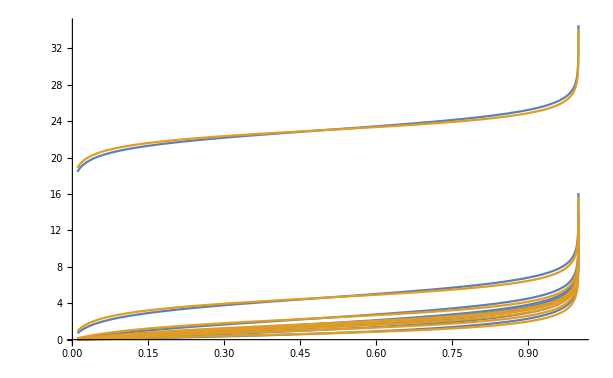

```mathematica
Plot[
{Table[
Norm[SphericalLogOursMap[xr,0.2,0.4,μ]["vector"]],{μ,{1,2,3,4,5,10,100,10^10}}
],
Table[
Norm[SphericalLogMap[xr,0.2,0.4,μ]["vector"]],{μ,{1,2,3,4,5,10,100,10^10}}
]
},{xr,0.01,.99999},PlotRange->All]
```

```mathematica
InvSphericalLogOursMap[x_,y_,z_,μ_]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=(Exp[r]-1)/(μ+Exp[r]-1);
drOverdx=μ/((1-xr)((μ-1)xr+1));
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)drOverdx r^2 Sin[θ])
|>
]
```

```mathematica
Manipulate[{
(InvSphericalLogOursMap@@Join[SphericalLogOursMap[x1,x2,x3,μ]["vector"],{μ}])["inv_jacobian"]*SphericalLogOursMap[x1,x2,x3,μ]["jacobian"],
(InvSphericalLogOursMap@@Join[SphericalLogOursMap[x1,x2,x3,μ]["vector"],{μ}])["xs"]-{x1,x2,x3}

}/.{x1->xm1,x2->xm2,x3->xm3,μ->μm},
{{xm1,0.2},0.,1.},
{{xm2,0.3},0.,1.},
{{xm3,0.4},0.,1.},
{{μm,3.0},0.,100.}
]
```

```mathematica
SphereVol[dim_,R_]:=π^(dim/2)/Gamma[dim/2+1] R^dim
```

```mathematica
chosenMu=10.;
Do[Print["Stats "<>ToString[statistics]<>" : "<>ToString[((NIntegrate[HeavisideTheta[
4-((SphericalLogOursMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦1⟧)^2
+(SphericalLogOursMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦2⟧)^2
+(SphericalLogOursMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦3⟧)^2
+(SphericalLogOursMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦1⟧)^2
+(SphericalLogOursMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦2⟧)^2
+(SphericalLogOursMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦3⟧)^2)]
SphericalLogOursMap[x1,x2,x3,chosenMu]⟦"jacobian"⟧SphericalLogOursMap[x4,x5,x6,chosenMu]⟦"jacobian"⟧,
{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1},{x6,0,1},
Method->"QuasiMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000
]-SphereVol[6,2])/SphereVol[6,2])*100.]<>"%"],{statistics,{100000,200000,300000}}]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 331.849 and 5.57528 for the integral and error estimates.

Stats 100000 : 0.337268%

NIntegrate::maxp: The integral failed to converge after 200000 integrand evaluations. NIntegrate obtained 331.128 and 3.86144 for the integral and error estimates.

Stats 200000 : 0.119147%

NIntegrate::maxp: The integral failed to converge after 300000 integrand evaluations. NIntegrate obtained 331.125 and 3.13358 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

Stats 300000 : 0.118424%

### Spherical LinLog

The parameter μ can tune how aggressively we want to probe the UV while still guaranteeing an asymptotic conformal jacobian behaviour of 1/(1-x).

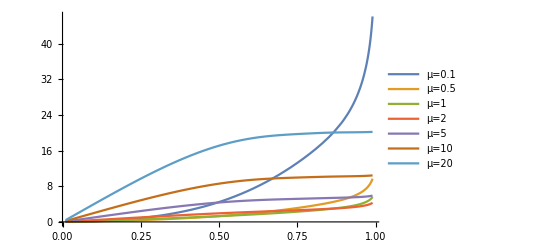

```mathematica
Plot[Evaluate@Table[μ(x1/(1-x1)Exp[-3/2(x1/(1-x1))]+(1-Exp[-x1/(1-x1)]))+1/μ Log[1+x1/(1-x1)](1-Exp[-(x1/(1-x1))]),{μ,{0.1,0.5,1,2,5,10,20}}],{x1,0.01,0.99},PlotLegends->Table["μ="<>ToString[μ],{μ,{0.1,0.5,1,2,5,10,20}}],PlotRange->All]
```

```mathematica
tt=Evaluate[((μ(x1/(1-x1)Exp[-3/2(x1/(1-x1))]+(1-Exp[-x1/(1-x1)]))+1/μ Log[1+x1/(1-x1)](1-Exp[-(x1/(1-x1))]))/.{μ->1})]
```

(ⅇ^(-(3 x1)/(2 (1-x1))) x1)/(1-x1)-ⅇ^(-x1/(1-x1))+(1-ⅇ^(-x1/(1-x1))) log(x1/(1-x1)+1)+1

```mathematica
FindRoot[((μ(x1/(1-x1)Exp[-3/2(x1/(1-x1))]+(1-Exp[-x1/(1-x1)]))+1/μ Log[1+x1/(1-x1)](1-Exp[-(x1/(1-x1))]))/.{μ->1})-1,{x1,0.5}]
```

{x1→0.406588}

```mathematica
myderivative=D[μ(x1/(1-x1)Exp[-3/2(x1/(1-x1))]+(1-Exp[-x1/(1-x1)]))+1/μ Log[1+x1/(1-x1)](1-Exp[-(x1/(1-x1))]),x1]//FullSimplify
```

(μ^2 ⅇ^((3 x1)/(2 (x1-1))) (5 x1-2)+2 ⅇ^(x1/(x1-1)) (x1-1) (μ^2+x1+log(1/(1-x1))-1)-2 (x1-1)^2)/(2 μ (x1-1)^3)

```mathematica
myderivative//InputForm
```

(-2*(-1 + x1)^2 + E^((3*x1)/(2*(-1 + x1)))*(-2 + 5*x1)*μ^2 + 2*E^(x1/(-1 + x1))*(-1 + x1)*(-1 + x1 + μ^2 + Log[(1 - x1)^(-1)]))/(2*(-1 + x1)^3*μ)

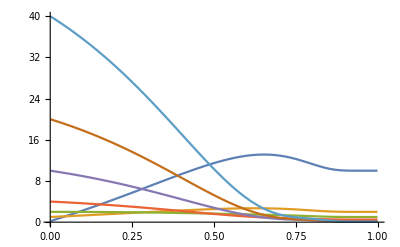

```mathematica
Plot[Evaluate[Table[(myderivative(1-x1)^1),{μ,{0.1,0.5,1,2,5,10,20}}]],{x1,0.001,0.999},PlotRange->All]
```

```mathematica
(-2*(-1 + x1)^2 + E^((3*x1)/(2*(-1 + x1)))*(-2 + 5*x1)*μ^2 + 2*E^(x1/(-1 + x1))*(-1 + x1)*(-1 + x1 + μ^2 + Log[(1 - x1)^(-1)]))/(2*(-1 + x1)^3*μ)
```

(μ^2 ⅇ^((3 x1)/(2 (x1-1))) (5 x1-2)+2 ⅇ^(x1/(x1-1)) (x1-1) (μ^2+x1+log(1/(1-x1))-1)-2 (x1-1)^2)/(2 μ (x1-1)^3)

```mathematica
SphericalLinLogMap[x1_,x2_,x3_,μ_]:=Module[
{r=μ(x1/(1-x1)Exp[-3/2(x1/(1-x1))]+(1-Exp[-x1/(1-x1)]))+1/μ Log[1+x1/(1-x1)](1-Exp[-(x1/(1-x1))]),θ=x2 π,ϕ=x3 2π,y,
drOverdx=(-2*(-1 + x1)^2 + E^((3*x1)/(2*(-1 + x1)))*(-2 + 5*x1)*μ^2 + 2*E^(x1/(-1 + x1))*(-1 + x1)*(-1 + x1 + μ^2 + Log[(1 - x1)^(-1)]))/(2*(-1 + x1)^3*μ)},
<|"vector"->{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ]
},
"jacobian"->(π) (2π)drOverdx r^2 Sin[θ]
|>
]
```

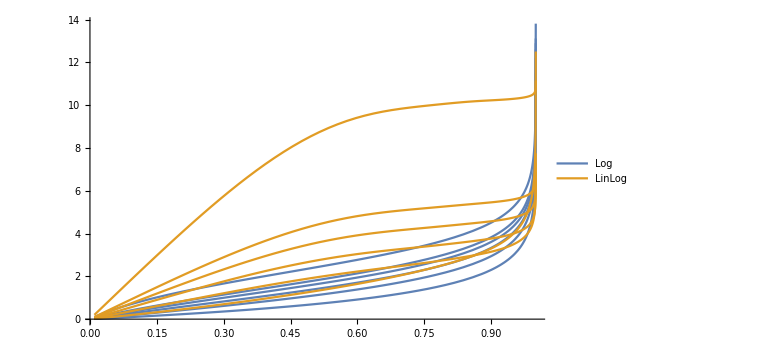

```mathematica
Plot[
{Table[
Norm[SphericalLogOursMap[xr,0.2,0.4,μ]["vector"]],{μ,{1,2,3,4,5,10}}
],
Table[
Norm[SphericalLinLogMap[xr,0.2,0.4,μ]["vector"]],{μ,{1,2,3,4,5,10}}
]
},{xr,0.01,.99999},PlotRange->All,PlotLegends->Placed[{"Log","LinLog"},Top],ImageSize->Large]
```

```mathematica
InvSphericalLinLogMap[x_,y_,z_,μ_]:=Module[
{r,θ,ϕ,xr,sphCoord,drOverdx},
sphCoord = ToSphericalCoordinates[{x,y,z}];
r=sphCoord⟦1⟧;
θ=sphCoord⟦2⟧;
ϕ=sphCoord⟦3⟧;
xr=x1/.FindRoot[Evaluate[(μ(x1/(1-x1)Exp[-3/2(x1/(1-x1))]+(1-Exp[-x1/(1-x1)]))+1/μ Log[1+x1/(1-x1)](1-Exp[-(x1/(1-x1))]))-r],{x1,0.5}];
drOverdx=(-2*(-1 + xr)^2 + E^((3*xr)/(2*(-1 + xr)))*(-2 + 5*xr)*μ^2 + 2*E^(xr/(-1 + xr))*(-1 + xr)*(-1 + xr + μ^2 + Log[(1 - xr)^(-1)]))/(2*(-1 + xr)^3*μ);
<|"xs"->{
xr,
θ/π,
Mod[ϕ,2π]/(2π)
},
"inv_jacobian"->1/((π) (2π)drOverdx r^2 Sin[θ])
|>
]
```

```mathematica
Manipulate[{
(InvSphericalLinLogMap@@Join[SphericalLinLogMap[x1,x2,x3,μ]["vector"],{μ}])["inv_jacobian"]*SphericalLinLogMap[x1,x2,x3,μ]["jacobian"],
(InvSphericalLinLogMap@@Join[SphericalLinLogMap[x1,x2,x3,μ]["vector"],{μ}])["xs"]-{x1,x2,x3}

},
{{x1,0.2},0.,1.},
{{x2,0.3},0.,1.},
{{x3,0.4},0.,1.},
{{μ,3.0},0.,100.}
]
```

```mathematica
SphereVol[dim_,R_]:=π^(dim/2)/Gamma[dim/2+1] R^dim
```

```mathematica
chosenMu=10.;
Do[Print["Stats "<>ToString[statistics]<>" : "<>ToString[((NIntegrate[HeavisideTheta[
4-((SphericalLinLogMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦1⟧)^2
+(SphericalLinLogMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦2⟧)^2
+(SphericalLinLogMap[x1,x2,x3,chosenMu]⟦"vector"⟧⟦3⟧)^2
+(SphericalLinLogMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦1⟧)^2
+(SphericalLinLogMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦2⟧)^2
+(SphericalLinLogMap[x4,x5,x6,chosenMu]⟦"vector"⟧⟦3⟧)^2)]
SphericalLinLogMap[x1,x2,x3,chosenMu]⟦"jacobian"⟧SphericalLinLogMap[x4,x5,x6,chosenMu]⟦"jacobian"⟧,
{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1},{x6,0,1},
Method->"QuasiMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000
]-SphereVol[6,2])/SphereVol[6,2])*100.]<>"%"],{statistics,{100000,200000,300000,1000000}}]
```

Stats 100000 : 4.66677%

Stats 200000 : -2.54943%

Stats 300000 : -0.0378807%

Stats 1000000 : 1.13183%

## Integrand definition

Let the integrator always display error message as it provides an estimate of the integral error.

```mathematica
Off[General::stop]
```

```mathematica
Integrand[k_,l_,p_,M_]:=((k.p)^2*l.p)/(((k+p).(k+p)+M^2)^2*((l+p).(l+p)+M^2)^2*((k+l).(k+l)+M^2))
```

```mathematica
Do[
Print[
"Stats "<>ToString[statistics]<>" : "<>ToString[
NIntegrate[Integrand[{kx,ky,kz},{lx,ly,lz},{2,2,2},1],
{kx,-∞,∞},{ky,-∞,∞},{kz,-∞,∞},
{lx,-∞,∞},{ly,-∞,∞},{lz,-∞,∞},
Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->statistics,MaxRecursion->1000]
]]
,{statistics,{1000000,5000000}}
]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2115.29 and 10.6351 for the integral and error estimates.

Stats 1000000 : -2115.29

$Aborted

## Probing the double UV limit

This is the first limit identified as problematic with the old disjoint parameterisation

### Momentum space

First let’s probe it in momentum space directly

```mathematica
MomSpaceProgression=Table[{UVscaleup,{{1,2,3},{4,5,6}}*10^UVscaleup},{UVscaleup,0.1,4.,0.01}];
```

```mathematica
Series[Integrand[{mx,mx,mx},{mx,mx,mx},{2,2,2},1],{mx,∞,0}]
```

O((1/mx)^7)

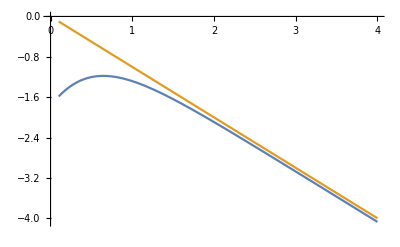

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,Norm[point⟦2⟧⟦1⟧]^3 Norm[point⟦2⟧⟦2⟧]^3 Integrand[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧,{2,2,2},1]]},
{point,MomSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
}
]
```

So yes, as expected this is dropping like -7, which means -1 when including the jacobian in momentum space which means it is integrable

### Disjoint Spherical space

Now let us study it in x-space using the disjoint parameterisation

```mathematica
DisjointXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalMap@@point⟦2⟧⟦1⟧)["xs"],(InvSphericalMap@@point⟦2⟧⟦2⟧)["xs"]}},
{point,MomSpaceProgression}
];
```

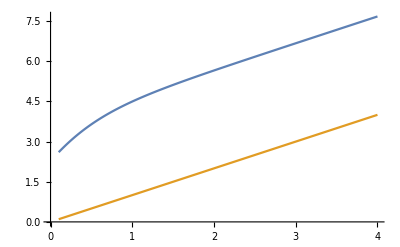

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalMap@@point⟦2⟧⟦1⟧)["jacobian"](SphericalMap@@point⟦2⟧⟦2⟧)["jacobian"]Integrand[(SphericalMap@@point⟦2⟧⟦1⟧)["vector"],(SphericalMap@@point⟦2⟧⟦2⟧)["vector"],{2,2,2},1]]},
{point,DisjointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->1}},
{point,MomSpaceProgression}
]
}
]
```

### Disjoint Spherical Log Weinzierl space

Now disjoin Log map

```mathematica
ChosenMu=10^10;
```

```mathematica
DisjointLogXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalLogMap@@Join[point⟦2⟧⟦1⟧,{ChosenMu}])["xs"],(InvSphericalLogMap@@Join[point⟦2⟧⟦2⟧,{ChosenMu}])["xs"]}},
{point,MomSpaceProgression}
];
```

```mathematica
aPoint=DisjointLogXSpaceProgression⟦300⟧;
{aPoint⟦1⟧,Log[10,(SphericalLogMap@@Join[aPoint⟦2⟧⟦1⟧,{ChosenMu}])["jacobian"](SphericalLogMap@@Join[aPoint⟦2⟧⟦2⟧,{ChosenMu}])["jacobian"]Integrand[(SphericalLogMap@@Join[aPoint⟦2⟧⟦1⟧,{ChosenMu}])["vector"],(SphericalLogMap@@Join[aPoint⟦2⟧⟦2⟧,{ChosenMu}])["vector"],{2,2,2},1]]}//InputForm
```

{3.0900000000000003, 6659.38096656836792519329996659429848115415`20.140239319397338}

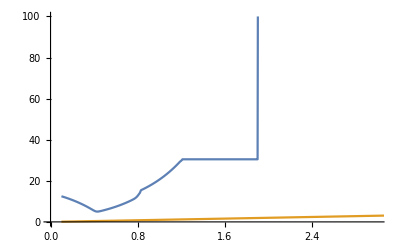

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalLogMap@@Join[point⟦2⟧⟦1⟧,{ChosenMu}])["jacobian"](SphericalLogMap@@Join[point⟦2⟧⟦2⟧,{ChosenMu}])["jacobian"]Integrand[(SphericalLogMap@@Join[point⟦2⟧⟦1⟧,{ChosenMu}])["vector"],(SphericalLogMap@@Join[point⟦2⟧⟦2⟧,{ChosenMu}])["vector"],{2,2,2},1]]},
{point,DisjointLogXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->1}},
{point,MomSpaceProgression}
]
},
PlotRange->{{0.,3.0},{0,100}}
]
```

This does not tell us anything because this parameterisation simply does not probe the UV basically

### Disjoint Spherical Log Ours space

Now disjoin Log map

```mathematica
ChosenMu=10;OverallScale=10000;
```

```mathematica
DisjointLogXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalLogOursMap@@Join[point⟦2⟧⟦1⟧/OverallScale,{ChosenMu}])["xs"],(InvSphericalLogOursMap@@Join[point⟦2⟧⟦2⟧/OverallScale,{ChosenMu}])["xs"]}},
{point,MomSpaceProgression}
];
```

```mathematica
MomSpaceProgression⟦-1⟧
```

{4.,(10000. | 20000. | 30000.
40000. | 50000. | 60000.)}

```mathematica
{
(SphericalLogOursMap@@Join[DisjointLogXSpaceProgression⟦-1⟧⟦2⟧⟦1⟧,{ChosenMu}])["vector"]*OverallScale,
(SphericalLogOursMap@@Join[DisjointLogXSpaceProgression⟦-1⟧⟦2⟧⟦2⟧,{ChosenMu}])["vector"]*OverallScale
}
```

(10000. | 20000. | 30000.
40000. | 50000. | 60000.)

```mathematica
aPoint=DisjointLogXSpaceProgression⟦50⟧;
{aPoint⟦1⟧,Log[10,
OverallScale(SphericalLogOursMap@@Join[aPoint⟦2⟧⟦1⟧,{ChosenMu}])["jacobian"]
OverallScale(SphericalLogOursMap@@Join[aPoint⟦2⟧⟦2⟧,{ChosenMu}])["jacobian"]
Integrand[
(SphericalLogOursMap@@Join[aPoint⟦2⟧⟦1⟧,{ChosenMu}])["vector"]*OverallScale,(SphericalLogOursMap@@Join[aPoint⟦2⟧⟦2⟧,{ChosenMu}])["vector"]*OverallScale,
{2,2,2},1]]}//InputForm
```

{0.59, -7.649057303076562}

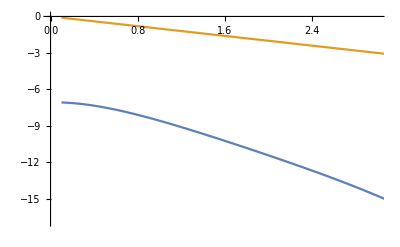

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
OverallScale(SphericalLogOursMap@@Join[point⟦2⟧⟦1⟧,{ChosenMu}])["jacobian"]OverallScale(SphericalLogOursMap@@Join[point⟦2⟧⟦2⟧,{ChosenMu}])["jacobian"]Integrand[(SphericalLogOursMap@@Join[point⟦2⟧⟦1⟧,{ChosenMu}])["vector"]*OverallScale,(SphericalLogOursMap@@Join[point⟦2⟧⟦2⟧,{ChosenMu}])["vector"]*OverallScale,{2,2,2},1]]},
{point,DisjointLogXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
},
PlotRange->{{0.,3.0},All}
]
```

This does not tell us anything because this parameterisation simply does not probe the UV basically

### Joint Spherical space

Let us now see how the join parameterisation remedies this

```mathematica
JointXSpaceProgression =Table[
{point⟦1⟧,(InvJointSphericalMap2Loop@@Join[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧])["xs"]},
{point,MomSpaceProgression}
];
```

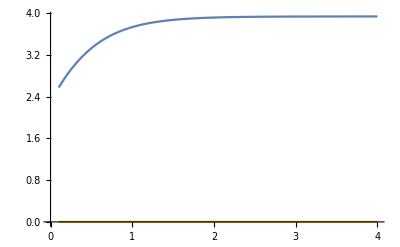

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(JointSphericalMap2Loop@@point⟦2⟧)["jacobian"]
Integrand[
(JointSphericalMap2Loop@@point⟦2⟧)["vectorA"],
(JointSphericalMap2Loop@@point⟦2⟧)["vectorB"],
{2,2,2},1]]},
{point,JointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->0}},
{point,MomSpaceProgression}
]
}
]
```

Yeah It goes like a constant now! :)

## Probing the single k-UV limit

First let’s probe it in momentum space directly

```mathematica
MomSpaceProgression=Table[{UVscaleup,{{1,2,3}*10^UVscaleup,{4,5,6}}},{UVscaleup,1.,15.,0.1}];
```

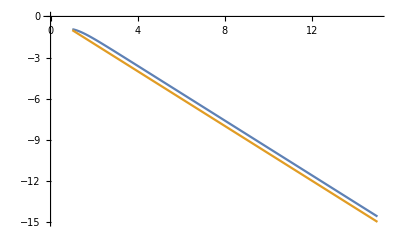

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,Norm[point⟦2⟧⟦1⟧]^3 Norm[point⟦2⟧⟦2⟧]^3 Integrand[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧,{2,2,2},1]]},
{point,MomSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
}
]
```

Old disjoint parameterisation

```mathematica
DisjointXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalMap@@point⟦2⟧⟦1⟧)["xs"],(InvSphericalMap@@point⟦2⟧⟦2⟧)["xs"]}},
{point,MomSpaceProgression}
];
```

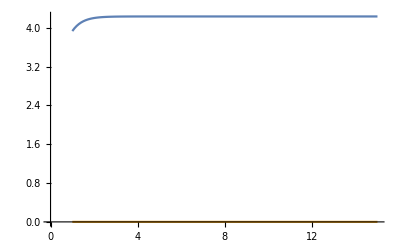

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalMap@@point⟦2⟧⟦1⟧)["jacobian"](SphericalMap@@point⟦2⟧⟦2⟧)["jacobian"]Integrand[(SphericalMap@@point⟦2⟧⟦1⟧)["vector"],(SphericalMap@@point⟦2⟧⟦2⟧)["vector"],{2,2,2},1]]},
{point,DisjointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-0}},
{point,MomSpaceProgression}
]
}
]
```

New joint parameterisation

```mathematica
JointXSpaceProgression =Table[
{point⟦1⟧,(InvJointSphericalMap2Loop@@Join[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧])["xs"]},
{point,MomSpaceProgression}
];
```

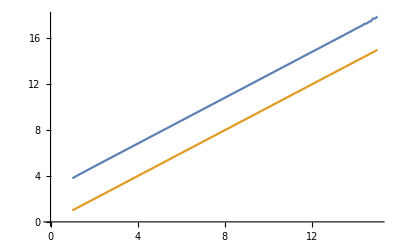

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(JointSphericalMap2Loop@@point⟦2⟧)["jacobian"]
Integrand[
(JointSphericalMap2Loop@@point⟦2⟧)["vectorA"],
(JointSphericalMap2Loop@@point⟦2⟧)["vectorB"],
{2,2,2},1]]},
{point,JointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->1}},
{point,MomSpaceProgression}
]
}
]
```

## Probing the single l-UV limit

First let’s probe it in momentum space directly

```mathematica
MomSpaceProgression=Table[{UVscaleup,{{1,2,3},{4,5,6}*10^UVscaleup}},{UVscaleup,1.,15.,0.1}];
```

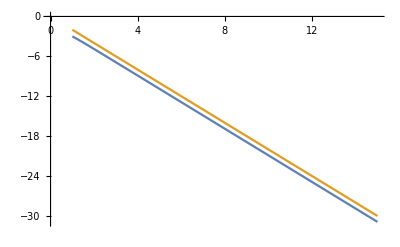

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,Norm[point⟦2⟧⟦1⟧]^3 Norm[point⟦2⟧⟦2⟧]^3 Integrand[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧,{2,2,2},1]]},
{point,MomSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-2}},
{point,MomSpaceProgression}
]
}
]
```

Old disjoint parameterisation

```mathematica
DisjointXSpaceProgression =Table[
{point⟦1⟧,{(InvSphericalMap@@point⟦2⟧⟦1⟧)["xs"],(InvSphericalMap@@point⟦2⟧⟦2⟧)["xs"]}},
{point,MomSpaceProgression}
];
```

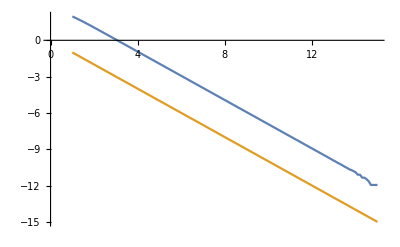

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(SphericalMap@@point⟦2⟧⟦1⟧)["jacobian"](SphericalMap@@point⟦2⟧⟦2⟧)["jacobian"]Integrand[(SphericalMap@@point⟦2⟧⟦1⟧)["vector"],(SphericalMap@@point⟦2⟧⟦2⟧)["vector"],{2,2,2},1]]},
{point,DisjointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->-1}},
{point,MomSpaceProgression}
]
}
]
```

New joint parameterisation

```mathematica
JointXSpaceProgression =Table[
{point⟦1⟧,(InvJointSphericalMap2Loop@@Join[point⟦2⟧⟦1⟧,point⟦2⟧⟦2⟧])["xs"]},
{point,MomSpaceProgression}
];
```

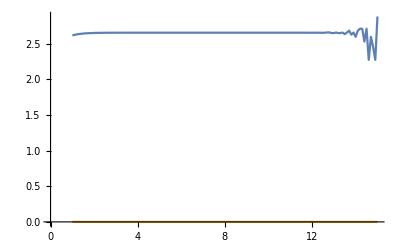

```mathematica
ListLinePlot[
{Table[
{point⟦1⟧,Log[10,
(JointSphericalMap2Loop@@point⟦2⟧)["jacobian"]
Integrand[
(JointSphericalMap2Loop@@point⟦2⟧)["vectorA"],
(JointSphericalMap2Loop@@point⟦2⟧)["vectorB"],
{2,2,2},1]]},
{point,JointXSpaceProgression}
],
Table[
{point⟦1⟧,((slope)*point⟦1⟧)/.{slope->0}},
{point,MomSpaceProgression}
]
}
]
```